```mathematica
(* Broadband pulses with fixed profile bandwidths ϵ = 0.9, 0.8, 0.7, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/3 *)
(* Error < 10^-3 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootBB;
err=0.001;
error=", error="<>ToString@err;
totalArea[rule_,sym_]:=Module[
{vars=rule/.Rule[a_,b_]->a},
area=Total[Abs[vars[[Length[vars]/2+1;;-1]]/.rule]];
If[sym,area=2area-vars[[-1]]/.rule];
area]
```

BB3; p=1, error=0.001

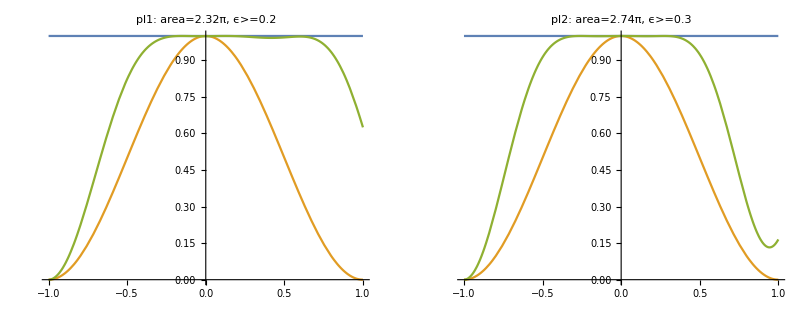

BB3; p=1/2, error=0.001

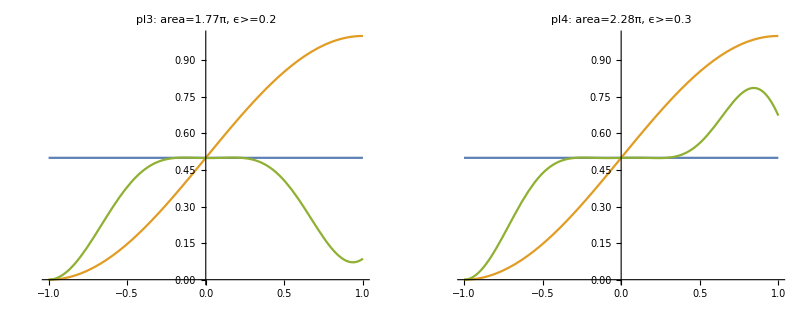

BB3; p=1/3, error=0.001

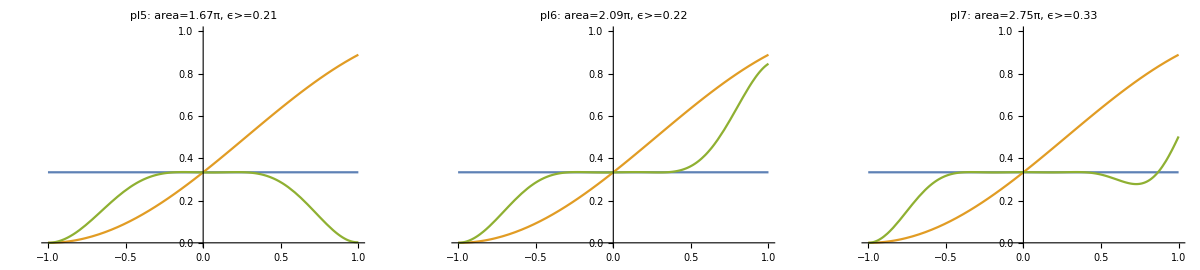

```mathematica
(*N=3*)
sequence=U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->0.8745,Δ2->0.0412,Δ3->-0.8559,Ω1->0.5573,Ω2->1.1661,Ω3->0.6002},"pl1"];
pl2=plt[1,{Δ1->-0.8977,Δ2->-0.0215,Δ3->0.8831,Ω1->0.6612,Ω2->1.3986,Ω3->0.6809},"pl2"];

pl3=plt[1/2,{Δ1->0.9828,Δ2->0.3254,Δ3->0.0795,Ω1->0.5375,Ω2->1.0217,Ω3->0.2139},"pl3"];
pl4=plt[1/2,{Δ1->0.0652,Δ2->0.5827,Δ3->0.9976,Ω1->0.7536,Ω2->1.0668,Ω3->0.4592},"pl4"];

pl5=plt[1/3,{Δ1->1.0168,Δ2->0.2070,Δ3->0.3766,Ω1->0.5348,Ω2->0.636,Ω3->0.5032},"pl5"];
pl6=plt[1/3,{Δ1->0.0668,Δ2->0.6899,Δ3->1.0046,Ω1->0.4358,Ω2->1.2057,Ω3->0.4531},"pl6"];
pl7=plt[1/3,{Δ1->1.0084,Δ2->0.7263,Δ3->0.5215,Ω1->0.3774,Ω2->0.9121,Ω3->1.4641},"pl7"];

GGrid[Text[Style["BB3; p=1"<> error,FontSize->20]],{{pl1,pl2,Null,Null}},ImageSize->Full]
GGrid[Text[Style["BB3; p=1/2"<> error,FontSize->20]],{{pl3,pl4,Null,Null}},ImageSize->Full]
GGrid[Text[Style["BB3; p=1/3"<> error,FontSize->20]],{{pl5,pl6,pl7,Null}},ImageSize->Full]
```

```mathematica
(*N=4, 5 DO NOT OFFER SMALLER PULSE AREAS THAN N=3 - however larger bandwidhts can be obtained*)
```

BB4; p=1, error=0.001

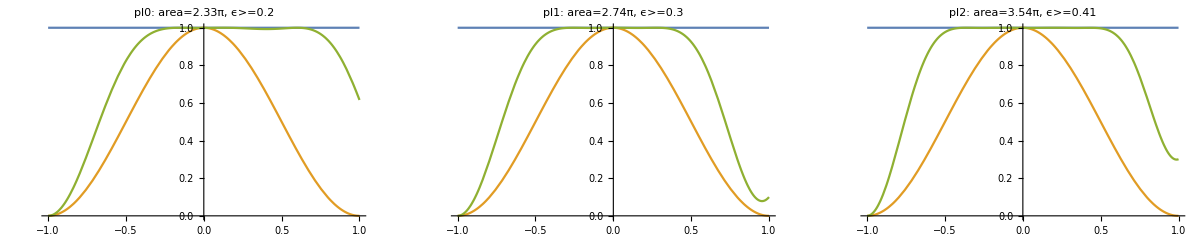

BB4; p=1/2, error=0.001

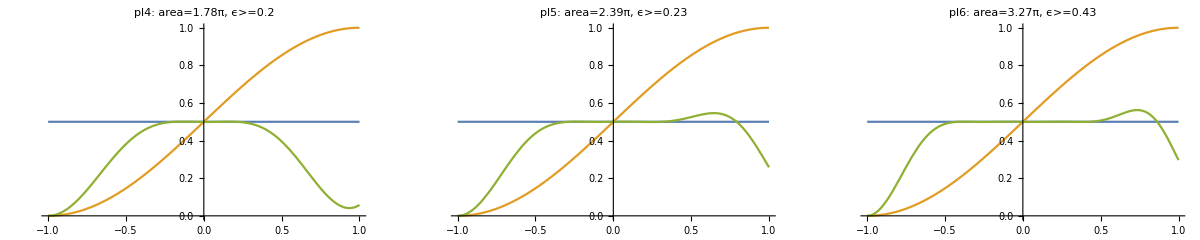

BB4; p=1/3, error=0.001

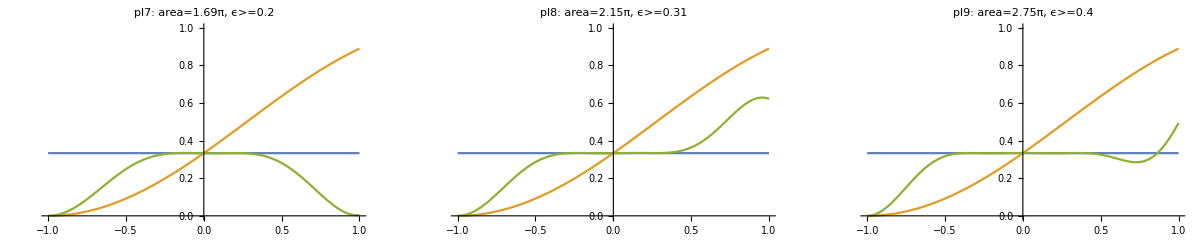

```mathematica
(*N=4*)
sequence=U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->0.8678,Δ2->0.0002,Δ3->-0.8662,Δ4->1.5612,Ω1->0.577,Ω2->1.1702,Ω3->0.5824,Ω4->0.0026},"pl0"];
pl2=plt[1,{Δ1->-0.8912,Δ2->0.0178,Δ3->0.6272,Δ4->0.1171,Ω1->0.6793,Ω2->1.4627,Ω3->0.3421,Ω4->0.2540},"pl1"];
pl3=plt[1,{Δ1->-0.9298,Δ2->-0.3701,Δ3->0.3028,Δ4->0.9062,Ω1->0.5272,Ω2->1.2095,Ω3->1.2416,Ω4->0.5621},"pl2"];

pl4=plt[1/2,{Δ1->0.4864,Δ2->0.4811,Δ3->0.1476,Δ4->0.2379,Ω1->0.2938,Ω2->0.2452,Ω3->0.5607,Ω4->0.6757},"pl4"];
pl5=plt[1/2,{Δ1->0.3920,Δ2->0.1524,Δ3->0.6466,Δ4->1.0003,Ω1->0.020,Ω2->0.975,Ω3->0.9818,Ω4->0.4105},"pl5"];
pl6=plt[1/2,{Δ1->1.0159,Δ2->0.7583,Δ3->0.3742,Δ4->0.1076,Ω1->0.3682,Ω2->0.9053,Ω3->1.0065,Ω4->0.9895},"pl6"];

pl7=plt[1/3,{Δ1->0.3041,Δ2->0.2530,Δ3->0.0622,Δ4->1.0542,Ω1->0.2269,Ω2->0.5010,Ω3->0.3866,Ω4->0.5750},"pl7"];
pl8=plt[1/3,{Δ1->0.3118,Δ2->0.4250,Δ3->0.1852,Δ4->0.9751,Ω1->0.8339,Ω2->0.6608,Ω3->0.2507,Ω4->0.4047},"pl8"];
pl9=plt[1/3,{Δ1->0.9742,Δ2->0.2313,Δ3->0.5439,Δ4->0.5178,Ω1->0.3538,Ω2->0.2477,Ω3->0.6938,Ω4->1.4571},"pl9"];

GGrid[Text[Style["BB4; p=1"<> error,FontSize->20]],{{pl1,pl2,pl3}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/2"<> error,FontSize->20]],{{pl4,pl5,pl6}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/3"<> error,FontSize->20]],{{pl7,pl8,pl9}},ImageSize->Full]
```

BB5 p=1, error=0.001

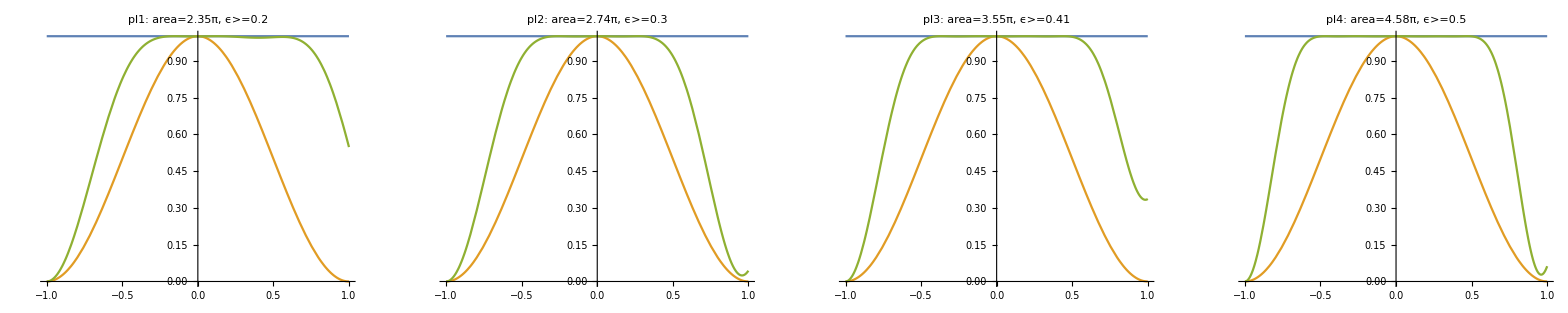

BB5 p=1/2, error=0.001

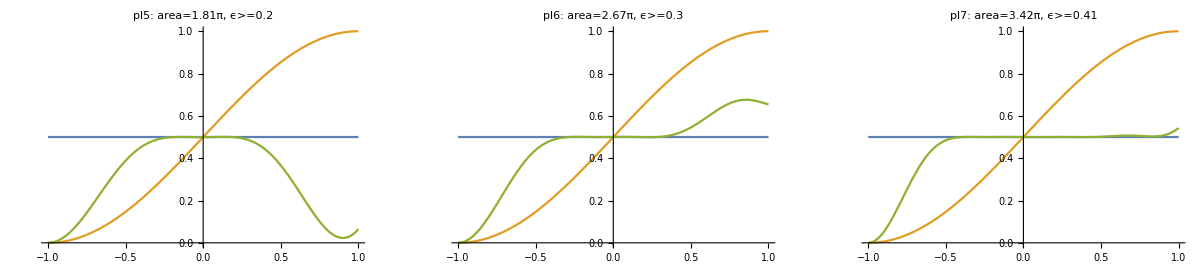

BB5 p=1/3, error=0.001

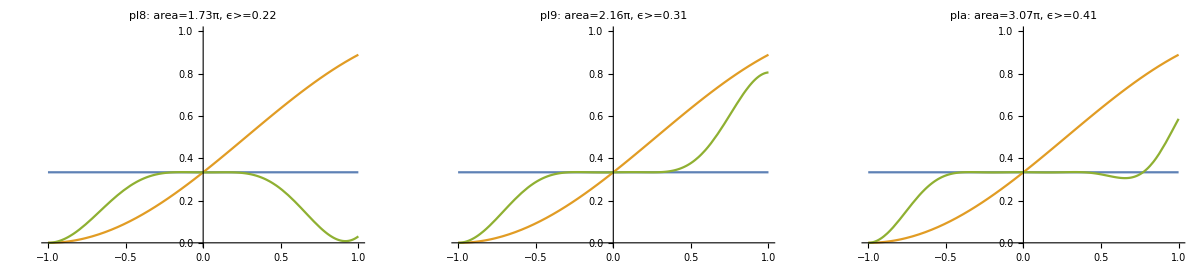

```mathematica
(*N=5*)
sequence=U[Δ5,Ω5].U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->-0.8721,Δ2->0.1202,Δ3->-0.1606,Δ4->0.7881,Δ5->0.0359,Ω1->0.6490,Ω2->0.8358,Ω3->0.2464,Ω4->0.4363,Ω5->0.1791},"pl1"];
pl2=plt[1,{Δ1->-0.4849,Δ2->-0.4808,Δ3->0.1958,Δ4->-0.1618,Δ5->0.9570,Ω1->0.3747,Ω2->0.4687,Ω3->0.5136,Ω4->0.6141,Ω5->0.7696},"pl2"];
pl3=plt[1,{Δ1->0.2251,Δ2->1.0073,Δ3->-0.2888,Δ4->-0.5765,Δ5->-0.4524,Ω1->1.17,Ω2->0.6333,Ω3->0.1326,Ω4->0.3234,Ω5->1.2938},"pl3"];
pl4=plt[1,{Δ1->-1.1615,Δ2->0.855,Δ3->-0.8186,Δ4->0.2691,Δ5->0.8572,Ω1->1.5025,Ω2->0.8622,Ω3->0.441,Ω4->0.6995,Ω5->1.0762},"pl4"];

pl5=plt[1/2,{Δ1->0.3778,Δ2->-0.1422,Δ3->0.3403,Δ4->0.373,Δ5->0.3872,Ω1->0.7082,Ω2->0.2393,Ω3->0.4120,Ω4->0.1583,Ω5->0.2954},"pl5"];
pl6=plt[1/2,{Δ1->-0.2089,Δ2->0.3928,Δ3->0.6148,Δ4->1.0254,Δ5->1.7488,Ω1->0.2502,Ω2->1.1182,Ω3->0.709,Ω4->0.3675,Ω5->0.2274},"pl6"];
pl7=plt[1/2,{Δ1->0.0411,Δ2->0.2244,Δ3->0.4736,Δ4->0.8172,Δ5->1.0249,Ω1->0.6575,Ω2->0.864,Ω3->0.8568,Ω4->0.7451,Ω5->0.2987},"pl7"];

pl8=plt[1/3,{Δ1->-0.0170,Δ2->0.3159,Δ3->0.6013,Δ4->0.0867,Δ5->0.4581,Ω1->0.0692,Ω2->0.1802,Ω3->0.2887,Ω4->0.4539,Ω5->0.7362},"pl8"];
pl9=plt[1/3,{Δ1->0.1010,Δ2->0.0139,Δ3->0.6603,Δ4->0.5762,Δ5->0.6085,Ω1->0.1549,Ω2->0.2763,Ω3->1.1779,Ω4->0.3450,Ω5->0.2026},"pl9"];
pla=plt[1/3,{Δ1->0.1377,Δ2->0.3909,Δ3->0.6942,Δ4->1.0692,Δ5->1.2835,Ω1->0.4163,Ω2->1.0951,Ω3->0.884,Ω4->0.517,Ω5->0.1621},"pla"];

GGrid[Text[Style["BB5 p=1"<> error,FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
GGrid[Text[Style["BB5 p=1/2"<> error,FontSize->20]],{{pl5,pl6,pl7,Null}},ImageSize->Full]
GGrid[Text[Style["BB5 p=1/3"<> error,FontSize->20]],{{pl8,pl9,pla,Null}},ImageSize->Full]
```